## 1.8.0

```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
<<EcoEvo`
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

EcoEvo Package Version 1.8.0 (June 16, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Aux[x]->{Equation:>x-0.5 x^2-x y /(x+1)},
Aux[y]->{Equation:>-m y+x y/(x+1)},
Parameters->{m}
}]
```

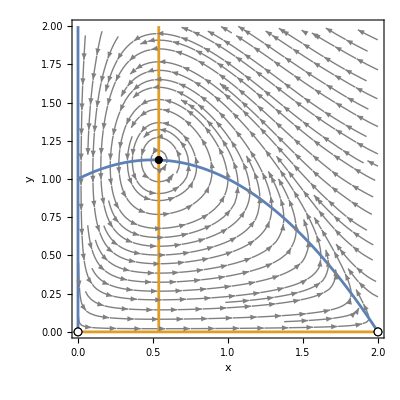

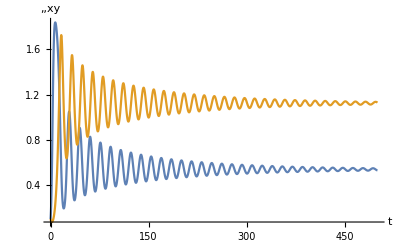

FindEcoCycle::relamp: Warning: EcoCycle relative amplitude 1.10202×10^-8 < MinAmplitude = 0.001.

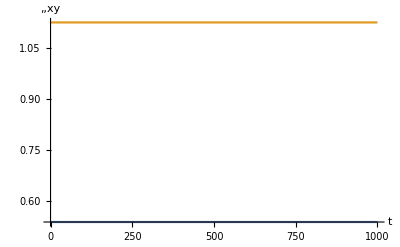

{x'→1.14463×10^-9,y'→-2.45664×10^-9}

```mathematica
m=0.35;
PlotEcoPhasePlane[{x,0,2},{y,0,2}]
sol=EcoSim[{x->0.1,y->0.1},500];
PlotDynamics[sol]
ec=FindEcoCycle[FinalSlice[sol]];
PlotDynamics[ec]
FinalDerivatives[ec]
```

```mathematica
RelativeAmplitude[ec]
```

{x→7.92132×10^-9,y→1.10202×10^-8}

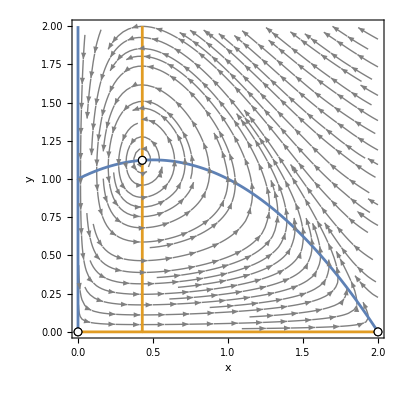

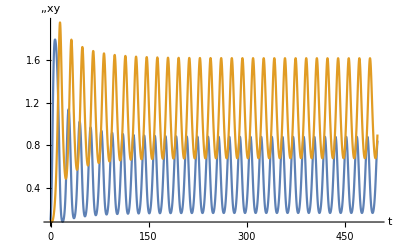

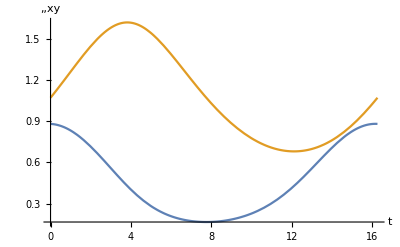

{x'→-0.00828357,y'→0.179955}

```mathematica
m=0.3;
PlotEcoPhasePlane[{x,0,2},{y,0,2}]
sol=EcoSim[{x->0.1,y->0.1},500];
PlotDynamics[sol]
ec=FindEcoCycle[FinalSlice[sol]];
PlotDynamics[ec]
FinalDerivatives[ec]
```

```mathematica
Clear[m]
```

```mathematica
trr=TrackEcoCycle[ec,{m,0.3,0.35,0.0001}]
```

FindEcoCycle::relamp: Warning: EcoCycle relative amplitude 0.0000443487 < MinAmplitude = 0.001.

FindEcoCycle::relamp: Warning: EcoCycle relative amplitude 0.0000630392 < MinAmplitude = 0.001.

FindEcoCycle::relamp: Warning: EcoCycle relative amplitude 0.0000442668 < MinAmplitude = 0.001.

General::stop: Further output of FindEcoCycle::relamp will be suppressed during this calculation.

TrackEcoCycle::err: FindEcoCycle failed at m=0.333334.

ParametricDynamics[…]

```mathematica
trl=TrackEcoCycle[ec,{m,0.3,0,-0.0000125},MaxExpansion->8]
```

NDSolve::ndsz: At t == 22.9125, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 25.8262, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 18.7736, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

TrackEcoCycle::err: FindEcoCycle failed at m=0.111213.

ParametricDynamics[…]

```mathematica
tr=JoinParametricDynamics[trl,trr]
```

ParametricDynamics[…]

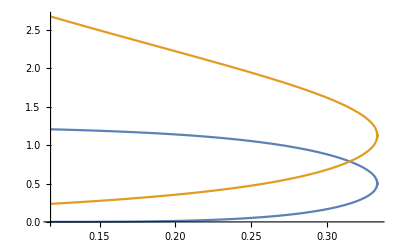

```mathematica
PlotRuleList[ExtremumValues[tr]]
```

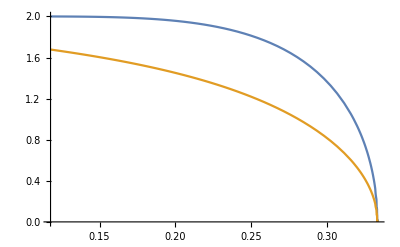

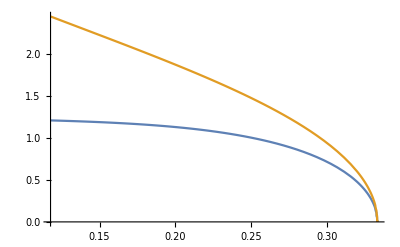

```mathematica
PlotRuleList[RelativeAmplitude[tr],PlotRange->{0,All}]
PlotRuleList[AbsoluteAmplitude[tr],PlotRange->{0,All}]
```

## 1.7.1

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.1 (December 30, 2022)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Aux[x]->{Equation:>x-0.5 x^2-x y /(x+1)},
Aux[y]->{Equation:>-m y+x y/(x+1)},
Parameters->{m}
}]
```

-Graphics-

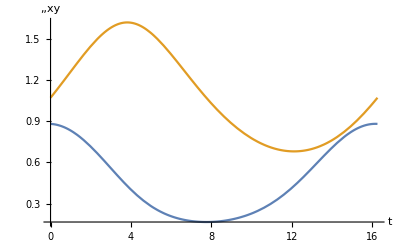

{x'→-0.00828357,y'→0.179955}

```mathematica
m=0.3;
PlotEcoPhasePlane[{x,0,2},{y,0,2}]
ec=FindEcoCycle[{x->0.1,y->0.1}];
PlotDynamics[ec]
FinalDerivatives[ec]
```

-Graphics-

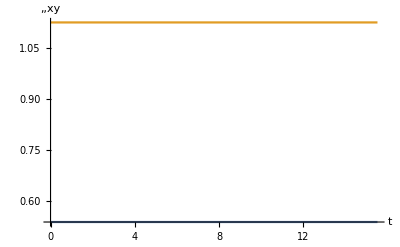

{x'→-4.6931×10^-7,y'→2.49523×10^-7}

```mathematica
m=0.35;
PlotEcoPhasePlane[{x,0,2},{y,0,2}]
ec=FindEcoCycle[{x->0.1,y->0.1}];
PlotDynamics[ec]
FinalDerivatives[ec]
```

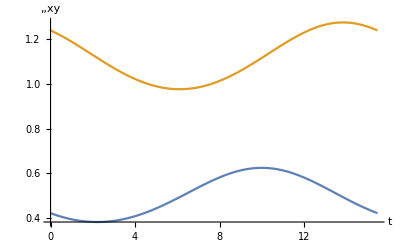

{x'→-0.0351107,y'→-0.0419667}

```mathematica
m=0.33;
ec=FindEcoCycle[{x->0.1,y->0.1}];
PlotDynamics[ec]
FinalDerivatives[ec]
```

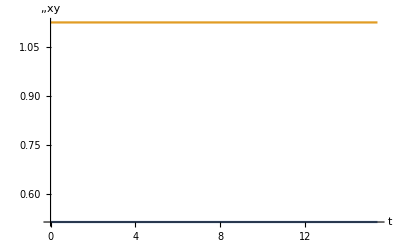

{x'→-1.90164×10^-6,y'→9.64337×10^-7}

```mathematica
m=0.34;
ec=FindEcoCycle[{x->0.1,y->0.1}];
PlotDynamics[ec]
FinalDerivatives[ec]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

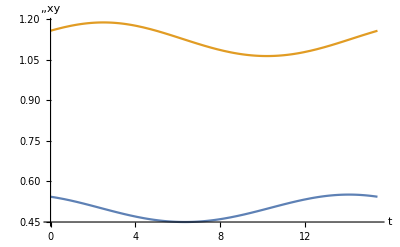

{x'→-0.0114798,y'→0.0221939}

```mathematica
m=0.333;
ec=FindEcoCycle[{x->0.1,y->0.1}];
PlotDynamics[ec]
FinalDerivatives[ec]
```

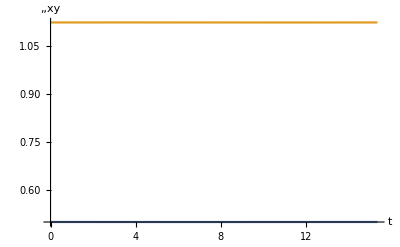

{x'→-3.53585×10^-6,y'→0.0000245312}

```mathematica
m=0.334;
ec=FindEcoCycle[{x->0.1,y->0.1}];
PlotDynamics[ec]
FinalDerivatives[ec]
```